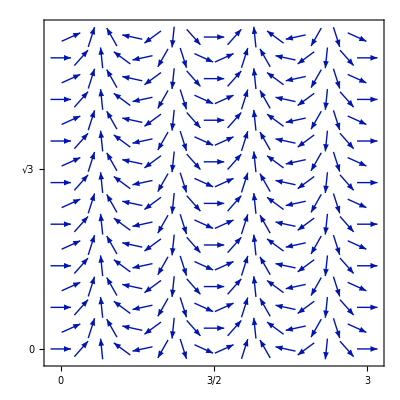

```mathematica
With[{q0=4 π/3{1,0},q1=4 π/3 RotationMatrix[-π/3*2].{1,0},q2=4 π/3*RotationMatrix[π/3*2].{1,0}},VectorPlot[Sum[{Cos[q.{x,y}],Sin[q.{x,y}]},{q,{q0}}],{x,0,3},{y,0,3},FrameTicks->{{0,3/2,6/2,9/2},{0,√3,2 √3}}]]
```

```mathematica
S[x_,y_]:=Block[{q0=4 π/3{-0,0},q1,q2},q1=RotationMatrix[π*2/3].q0;q2=RotationMatrix[π*4/3].q0;Sum[{Cos[q.{x,y}],Sin[q.{x,y}]},{q,{q0(*,q1,q2*)}}]]
```

```mathematica
S[x_,y_]:=Block[{q0=4 π/3{1,0},q1,q2},q1=RotationMatrix[π*2/3].q0;q2=RotationMatrix[π*4/3].q0;Sum[{Cos[q.{x,y}],Sin[q.{x,y}]},{q,{q0,q1,q2}}]]
```

```mathematica
S[0,0]
```

{1,0}

```mathematica
M1[x_,y_,χ_]:=Block[{q1=4 π/3{1,0},q2=4 π/3{1,0}.RotationMatrix[2π/3],q3=4 π/3{1,0}.RotationMatrix[4π/3],mat},mat=Sum[Cos[q.{x,y}]*PauliMatrix[1]+Sin[χ*q.{x,y}]*PauliMatrix[2],{q,{q1,q2,q3}}];{Re@(mat[[2,1]]),Im@(mat[[2,1]])}]
```

```mathematica
M1orig[x_,y_,χ_]:=Block[{q1=4 π/3{1,0},q2=4 π/3{1,0}.RotationMatrix[2π/3],q3=4 π/3{1,0}.RotationMatrix[4π/3],mat},mat=Sum[Cos[q.{x,y}]*PauliMatrix[1]+Sin[χ*q.{x,y}]*PauliMatrix[2],{q,{q1,q2,q3}}];{Re@(Exp[I*2*q2.{x,y}]mat[[2,1]]),Im@(Exp[I*2*q2.{x,y}]mat[[2,1]])}]
```

```mathematica
M0[x_,y_]:=Block[{q0={0,0},q1=4 π/3{1,0},q2=4 π/3{1,0}.RotationMatrix[2π/3],q3=4 π/3{1,0}.RotationMatrix[4π/3],mat},mat=Sum[Cos[q.{x,y}]*PauliMatrix[1]+Sin[χ*q.{x,y}]*PauliMatrix[2],{q,{q0}}];{Re@(mat[[2,1]]),Im@(mat[[2,1]])}]
```

```mathematica
M0orig[x_,y_]:=Block[{q0={0,0},q1=4 π/3{1,0},q2=4 π/3{1,0}.RotationMatrix[2π/3],q3=4 π/3{1,0}.RotationMatrix[4π/3],mat},mat=Sum[Cos[q.{x,y}]*PauliMatrix[1]+Sin[χ*q.{x,y}]*PauliMatrix[2],{q,{q0}}];{Re@(Exp[I*2*q2.{x,y}]mat[[2,1]]),Im@(Exp[I*2*q2.{x,y}]mat[[2,1]])}]
```

```mathematica
M1[1.,1.]
```

{-0.433106,0.634724}

```mathematica
M1[0.,0.]
```

{3.,0.}

```mathematica
pts=Table[aM1*h1+aM2*h2,{h1,0,3},{h2,-1,3}];M1list=Table[{aM1*h1+aM2*h2,M1[#1,#2,1]&@@(aM1*h1+aM2*h2)},{h1,0,3},{h2,-1,3}];
ptsf=Table[aM1*h1+aM2*h2,{h1,0,3,0.1},{h2,-1,3,0.1}];M1listf=Table[{aM1*h1+aM2*h2,M1[#1,#2,1]&@@(aM1*h1+aM2*h2)},{h1,0,3,0.1},{h2,-1,3,0.1}];
```

```mathematica
pts=Table[aM1*h1+aM2*h2,{h1,0,3},{h2,-1,3}];M1origlist=Table[{aM1*h1+aM2*h2,M1orig[#1,#2,1]&@@(aM1*h1+aM2*h2)},{h1,0,3},{h2,-1,3}];
ptsf=Table[aM1*h1+aM2*h2,{h1,0,3,0.1},{h2,-1,3,0.1}];M1origlistf=Table[{aM1*h1+aM2*h2,M1orig[#1,#2,1]&@@(aM1*h1+aM2*h2)},{h1,0,3,0.1},{h2,-1,3,0.1}];
```

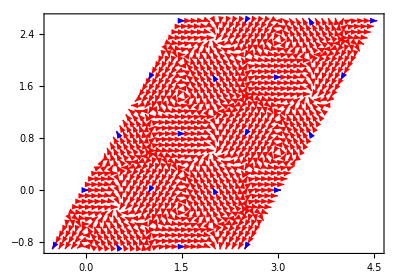

```mathematica
ListVectorPlot[{Flatten[M1listf,1],Flatten[M1list,1]},VectorPoints->All,AspectRatio->Automatic,VectorStyle->{Red, Blue},VectorColorFunction->None]
```

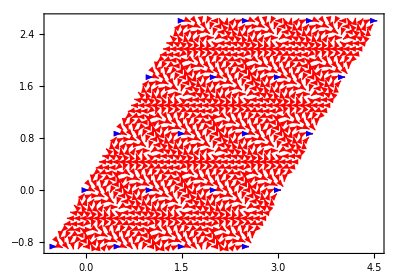

```mathematica
ListVectorPlot[{Flatten[M1origlistf,1],Flatten[M1origlist,1]},VectorPoints->All,AspectRatio->Automatic,VectorStyle->{Red, Blue},VectorColorFunction->None]
```

```mathematica
pts=Table[aM1*h1+aM2*h2,{h1,0,3},{h2,-1,3}];M1list=Table[{aM1*h1+aM2*h2,M1[#1,#2,-1]&@@(aM1*h1+aM2*h2)},{h1,0,3},{h2,-1,3}];
ptsf=Table[aM1*h1+aM2*h2,{h1,0,3,0.1},{h2,-1,3,0.1}];M1listf=Table[{aM1*h1+aM2*h2,M1[#1,#2,-1]&@@(aM1*h1+aM2*h2)},{h1,0,3,0.1},{h2,-1,3,0.1}];
```

```mathematica
pts=Table[aM1*h1+aM2*h2,{h1,0,3},{h2,-1,3}];M1origlist=Table[{aM1*h1+aM2*h2,M1orig[#1,#2,-1]&@@(aM1*h1+aM2*h2)},{h1,0,3},{h2,-1,3}];
ptsf=Table[aM1*h1+aM2*h2,{h1,0,3,0.1},{h2,-1,3,0.1}];M1origlistf=Table[{aM1*h1+aM2*h2,M1orig[#1,#2,-1]&@@(aM1*h1+aM2*h2)},{h1,0,3,0.1},{h2,-1,3,0.1}];
```

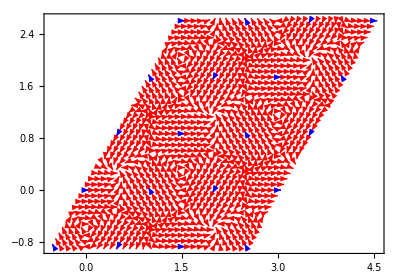

```mathematica
ListVectorPlot[{Flatten[M1listf,1],Flatten[M1list,1]},VectorPoints->All,AspectRatio->Automatic,VectorStyle->{Red, Blue},VectorColorFunction->None]
```

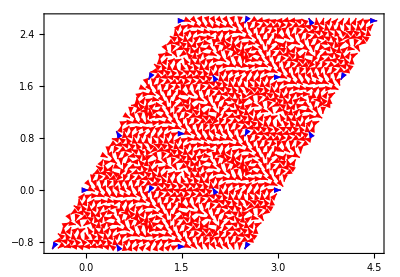

```mathematica
ListVectorPlot[{Flatten[M1origlistf,1],Flatten[M1origlist,1]},VectorPoints->All,AspectRatio->Automatic,VectorStyle->{Red, Blue},VectorColorFunction->None]
```

```mathematica
pts=Table[aM1*h1+aM2*h2,{h1,0,3},{h2,-1,3}];M0list=Table[{aM1*h1+aM2*h2,M0[#1,#2]&@@(aM1*h1+aM2*h2)},{h1,0,3},{h2,-1,3}];
ptsf=Table[aM1*h1+aM2*h2,{h1,0,3,0.1},{h2,-1,3,0.1}];M0listf=Table[{aM1*h1+aM2*h2,M0[#1,#2]&@@(aM1*h1+aM2*h2)},{h1,0,3,0.1},{h2,-1,3,0.1}];
```

```mathematica
pts=Table[aM1*h1+aM2*h2,{h1,0,3},{h2,-1,3}];M0origlist=Table[{aM1*h1+aM2*h2,M0orig[#1,#2]&@@(aM1*h1+aM2*h2)},{h1,0,3},{h2,-1,3}];
ptsf=Table[aM1*h1+aM2*h2,{h1,0,3,0.1},{h2,-1,3,0.1}];M0origlistf=Table[{aM1*h1+aM2*h2,M0orig[#1,#2]&@@(aM1*h1+aM2*h2)},{h1,0,3,0.1},{h2,-1,3,0.1}];
```

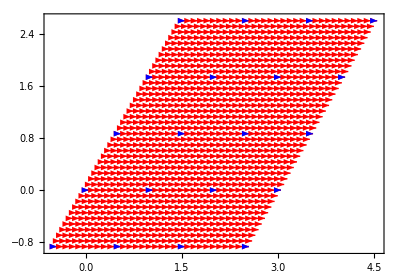

```mathematica
ListVectorPlot[{Flatten[M0listf,1],Flatten[M0list,1]},VectorPoints->All,AspectRatio->Automatic,VectorStyle->{Red, Blue},VectorColorFunction->None]
```

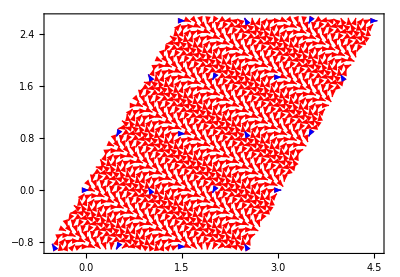

```mathematica
ListVectorPlot[{Flatten[M0origlistf,1],Flatten[M0origlist,1]},VectorPoints->All,AspectRatio->Automatic,VectorStyle->{Red, Blue},VectorColorFunction->None]
```

```mathematica
aM1={1,0};aM2={1/2,(√3)/2};
```

```mathematica
pts=Table[aM1*h1+aM2*h2,{h1,0,3},{h2,-1,3}];Slist=Table[{aM1*h1+aM2*h2,S@@(aM1*h1+aM2*h2)},{h1,0,3},{h2,-1,3}];
```

```mathematica
ptsf=Table[aM1*h1+aM2*h2,{h1,0,3,0.1},{h2,-1,3,0.1}];Slistf=Table[{aM1*h1+aM2*h2,S@@(aM1*h1+aM2*h2)},{h1,0,3,0.1},{h2,-1,3,0.1}];
```

```mathematica
Slistfmod=Table[Flatten@{aM1*h1+aM2*h2,Norm[S@@(aM1*h1+aM2*h2)]},{h1,0,5,0.05},{h2,0,5,0.05}];
```

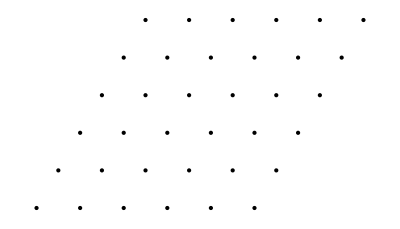

```mathematica
Graphics[Point/@pts]
```

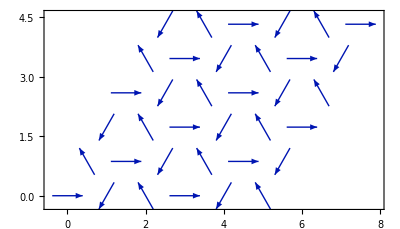

```mathematica
ListVectorPlot[Flatten[Slist,1],VectorPoints->All,AspectRatio->Automatic]
```

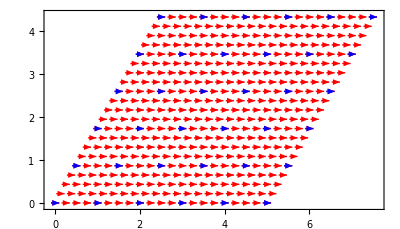

```mathematica
ListVectorPlot[{Flatten[Slistf,1],Flatten[Slist,1]},VectorPoints->All,AspectRatio->Automatic,VectorStyle->{Red, Blue},VectorColorFunction->None]
```

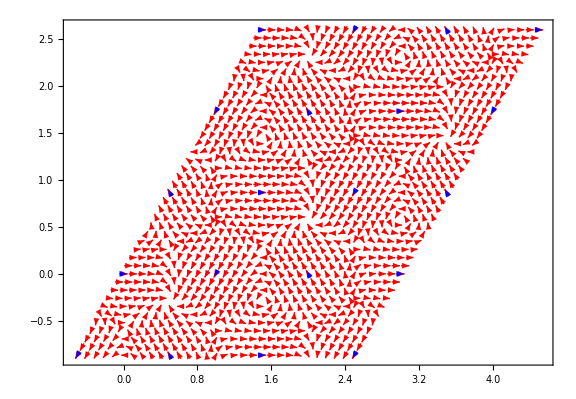

```mathematica
ListVectorPlot[{Flatten[Slistf,1],Flatten[Slist,1]},VectorPoints->All,AspectRatio->Automatic,VectorStyle->{Red, Blue},VectorColorFunction->None,ImageSize->Large,VectorScaling->Automatic]
```

```mathematica
ListDensityPlot[Flatten[Slistfmod,1],AspectRatio->Automatic,PlotLegends->Automatic]
```

-Graphics-